# Donw-converted photon bandwidths as a function of the pulse duration

### Libraries

```mathematica
Needs["ParametricDownConversion`"]
```

```mathematica
?"ParametricDownConversion`*"
```

### Parameters

```mathematica
(* Wavelengths in m and corresponding ω*)
λp=775.*10^-9;
λs=λp*2.;
λi=λp*2.;
ωp=LambdaToOmega[λp];
ωs=LambdaToOmega[λs];
ωi=LambdaToOmega[λi];
```

```mathematica
(* Temperature of the crystal *)
temperature=25;
```

```mathematica
(* Import crystal domains and compute boundaries positions *)
trueCrystalWalls=ImportCrystal["data_crystals/aKTP_30mm_775nm_Gaussian_4.7sigma.xlsx",NotebookDirectory[]];
trueCrystalLength=trueCrystalWalls⟦-1⟧;
```

```mathematica
(* Poling suggested by Raicol for phase-matching around 40 degrees *)
truePolingPeriod=0.000046175;
computedPolingPeriod=KTPPolingPeriod[λs,λi,λp,temperature];
```

```mathematica
(* Rescale walls to have the PMF centred at 1550nm *)
crystalWalls=trueCrystalWalls*computedPolingPeriod/truePolingPeriod;
crystalLength=crystalWalls⟦-1⟧;
```

```mathematica
(* Find the τ parameter from the pulse length *)
pulseLength=1.4*10^-12;
tauPump=TauFromPulseLength[pulseLength];
```

```mathematica
(* Compute list of frequencies for the signal and idler: range of ~9nm, 101x101 matrix *)
deltaOmega=7.*10^12;
signalFrequencies=FrequencyList[ωs-deltaOmega,ωs+deltaOmega,(2deltaOmega)/100];
idlerFrequencies=FrequencyList[ωi-deltaOmega,ωi+deltaOmega,(2deltaOmega)/100];
freqsList=FrequencyMatrix[signalFrequencies,idlerFrequencies];
pumpFrequencies=FrequencyList[ωp-deltaOmega,ωp+deltaOmega,deltaOmega/100];
```

```mathematica
timeRange=DeleteDuplicates[Sort[Range[-7*10^-12,7*10^-12,0.1*10^-12]~Join~Range[-1*10^-12,1*10^-12,0.02*10^-12]]];
```

### Plot options

```mathematica
SetOptions[Plot,
PlotRange->All,
PlotStyle->{RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]]}
,Frame->True
,FrameStyle->Black
,LabelStyle->{18,Black,font}
,ImageSize->Medium]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→GrayLevel[0],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Medium,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{18,GrayLevel[0],FontFamily→YuMincho},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotLabel→None,PlotLabels→None,PlotLayout→Automatic,PlotLegends→None,PlotPoints→Automatic,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→{RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]]},PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
SetOptions[ListPlot,
PlotRange->All
,PlotStyle->{RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]]}
,Frame->True
,FrameStyle->Black
,LabelStyle->{18,Black,font}
,ImageSize->Medium]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→GrayLevel[0],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Medium,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{18,GrayLevel[0],FontFamily→YuMincho},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→{RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]]},PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
SetOptions[ListLinePlot,
PlotRange->All,
PlotStyle->{RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]]}
,Frame->True
,FrameStyle->Black
,LabelStyle->{18,Black,font}
,ImageSize->Medium]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→GrayLevel[0],FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Medium,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→True,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{18,GrayLevel[0],FontFamily→YuMincho},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotHighlighting→Automatic,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→{RGBColor[Rational[81, 256], Rational[45, 256], Rational[43, 128]],RGBColor[Rational[169, 256], Rational[59, 256], Rational[27, 64]]},PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
SetOptions[ListDensityPlot,
FrameLabel->{"λ_s","λ_i",None,None},
LabelStyle->{18,Black,font},
PlotRange->All,
ColorFunction->CustomColorFunction,
ImageSize->Medium,
MeshStyle->Directive[White,Opacity[0.2]]]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→(Blend[rocketColors,#1 1]&),ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→{λ_s,λ_i,None,None},FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Medium,ImageSizeRaw→Automatic,InterpolationOrder→None,LabelStyle→{18,GrayLevel[0],FontFamily→YuMincho},LightingAngle→None,MaxPlotPoints→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshStyle→Directive[GrayLevel[1],Opacity[0.2]],Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLayout→Automatic,PlotLegends→None,PlotRange→All,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},VertexColors→Automatic}

## Define Joint Spectral Amplitude

### Sech PEF

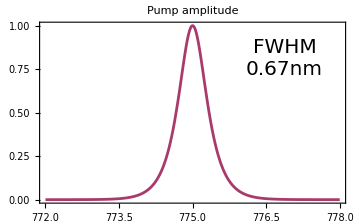

```mathematica
Plot[PEFSech[0,LambdaToOmega[lambda*10^-9],ωp,tauPump],{lambda,772,778}
,PlotRange->All
,PlotLabel->"Pump amplitude"
,Epilog->Inset[Style["FWHM\n"<>ToString@NumberForm[10^9 DeltaOmegaToDeltaLambda[SpectralAMPfwhmSech[TauFromPulseLength[pulseLength]],λp],{3,2}]<>"nm",20],Scaled[{0.8,0.8}]]
]
```

```mathematica
pumpMatrix=PEFMatrix[freqsList,PEFSech,ωp,TauFromPulseLength[pulseLength]];
```

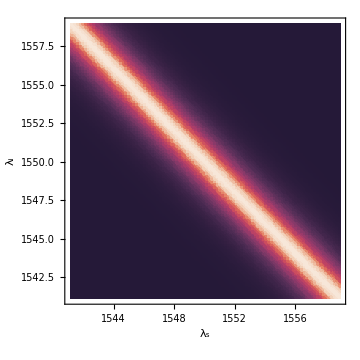

```mathematica
ListDensityPlot[MatrixToLambdas[pumpMatrix,10^9],PlotRangePadding->None]
```

### Import PMF

```mathematica
(* Calculate the PMF in the Δk space *)
```

```mathematica
dkValues=Range[134000,138000,10];
```

```mathematica
pmfFunction=PhaseMatchingFunction[dkValues,crystalWalls];
```

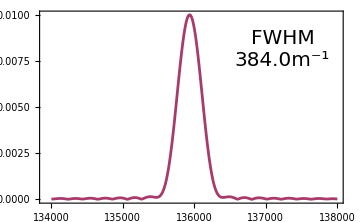

```mathematica
ListPlot[Abs@pmfFunction
,Joined->True
,Epilog->Inset[Style["FWHM\n"<>ToString@NumberForm[FWHM[Abs@pmfFunction],{3,1}]<>"m^-1",20],Scaled[{0.8,0.8}]]
]
```

```mathematica
dkMatrix=DeltaKMatrix[freqsList,KTPRefIndY,KTPRefIndZ,KTPRefIndY];
```

```mathematica
pmfMatrix=PMFMatrix[dkMatrix,crystalWalls];
```

## Alternating pulse duration on the order of ps

```mathematica
pulseLength=Range[1.3*10^-12,1.5*10^-12,0.1*10^-12];
pumpMatrix=PEFMatrix[freqsList,PEFGauss,ωp,SigmaFromPulseLength[#]]&/@pulseLength;
jsaMatrix=JSAMatrix[#,pmfMatrix]&/@pumpMatrix;
```

```mathematica
photonSpectra=MarginalSpectra[#]&/@jsaMatrix;
```

```mathematica
signalSpectrumLambda={OmegaToLambda@#⟦1⟧⟦;;,1⟧*10^9,Abs@#⟦1⟧⟦;;,2⟧}&/@photonSpectra;
idlerSpectrumLambda={OmegaToLambda@#⟦2⟧⟦;;,1⟧*10^9,Abs@#⟦2⟧⟦;;,2⟧}&/@photonSpectra;
```

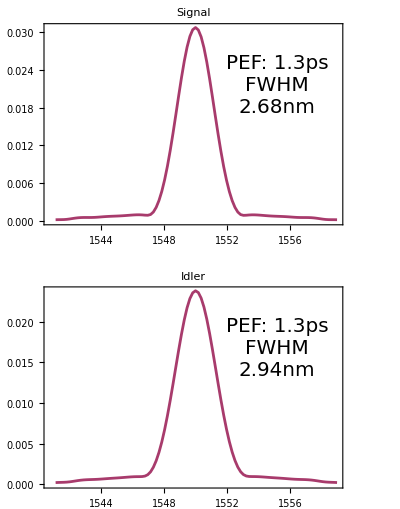
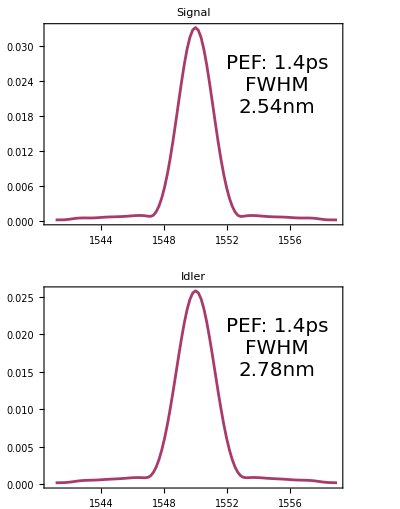
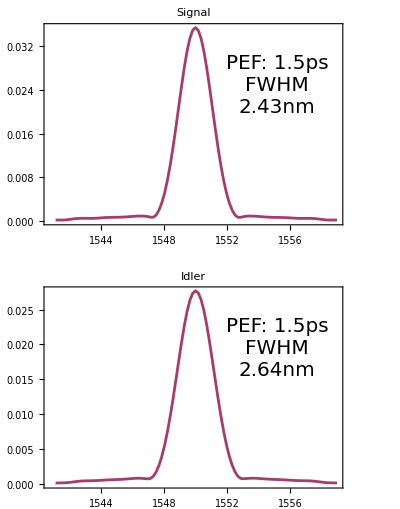

```mathematica
Table[
GraphicsColumn[
{ListPlot[signalSpectrumLambda⟦i⟧ᵀ
,Joined->True,PlotLabel->"Signal",Epilog->Inset[Style["PEF: "<>ToString@NumberForm[pulseLength⟦i⟧*10^12]<>"ps"<>"\nFWHM\n"<>ToString@NumberForm[FWHM[signalSpectrumLambda⟦i⟧ᵀ],{3,2}]<>"nm",20],Scaled[{0.78,0.7}]]]
,
ListPlot[idlerSpectrumLambda⟦i⟧ᵀ
,Joined->True,PlotLabel->"Idler",Epilog->Inset[Style["PEF: "<>ToString@NumberForm[pulseLength⟦i⟧*10^12]<>"ps"<>"\nFWHM\n"<>ToString@NumberForm[FWHM[idlerSpectrumLambda⟦i⟧ᵀ],{3,2}]<>"nm",20],Scaled[{0.78,0.7}]]]}
]
,{i,1,Length[pulseLength]}]
```

## Alternating pulse duration on the order of fs

```mathematica
pulseLength=Range[500*10^-15,1*10^-12,100*10^-15];
pumpMatrix=PEFMatrix[freqsList,PEFGauss,ωp,SigmaFromPulseLength[#]]&/@pulseLength;
jsaMatrix=JSAMatrix[#,pmfMatrix]&/@pumpMatrix;
```

```mathematica
photonSpectra=MarginalSpectra[#]&/@jsaMatrix;
```

```mathematica
signalSpectrumLambda={OmegaToLambda@#⟦1⟧⟦;;,1⟧*10^9,Abs@#⟦1⟧⟦;;,2⟧}&/@photonSpectra;
idlerSpectrumLambda={OmegaToLambda@#⟦2⟧⟦;;,1⟧*10^9,Abs@#⟦2⟧⟦;;,2⟧}&/@photonSpectra;
```

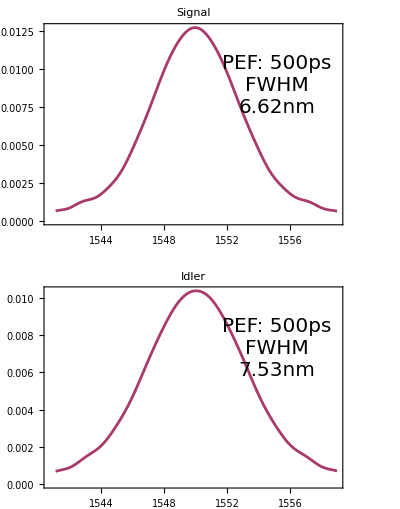
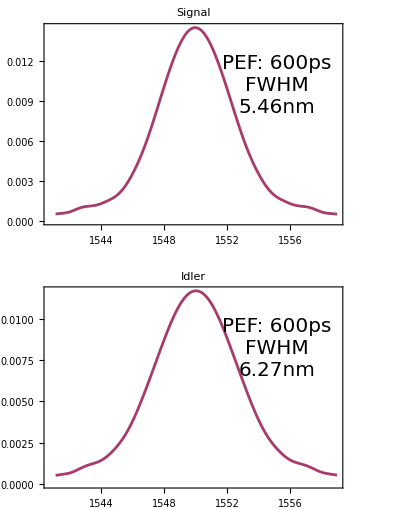
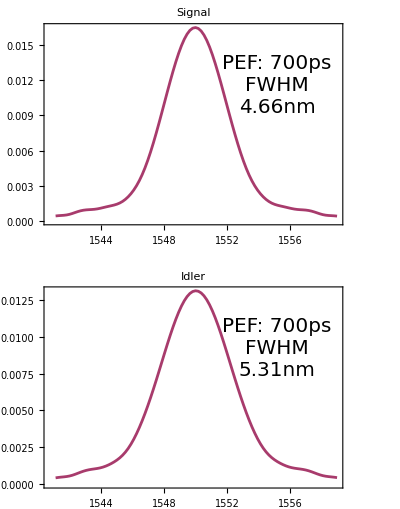
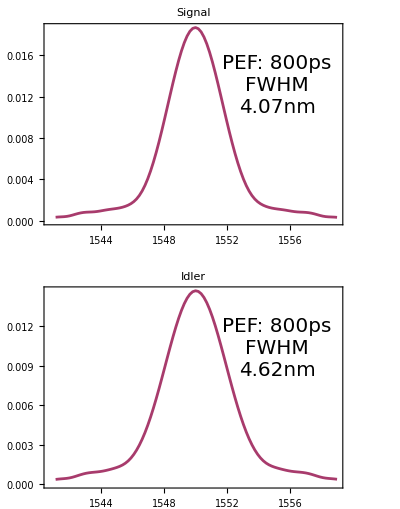
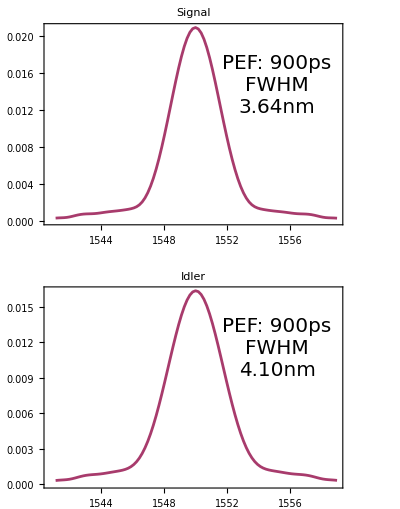
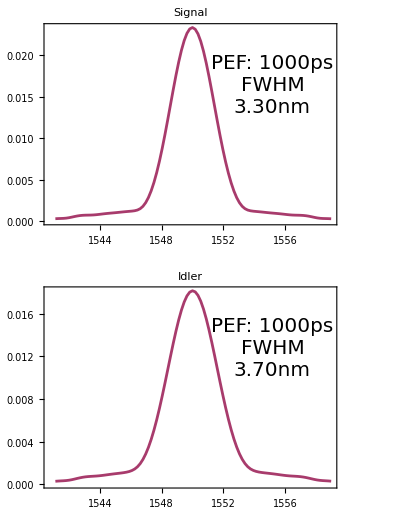

```mathematica
Table[
GraphicsColumn[
{ListPlot[signalSpectrumLambda⟦i⟧ᵀ
,Joined->True,PlotLabel->"Signal",Epilog->Inset[Style["PEF: "<>ToString@NumberForm[pulseLength⟦i⟧*10^15]<>"ps"<>"\nFWHM\n"<>ToString@NumberForm[FWHM[signalSpectrumLambda⟦i⟧ᵀ],{3,2}]<>"nm",20],Scaled[{0.78,0.7}]]]
,
ListPlot[idlerSpectrumLambda⟦i⟧ᵀ
,Joined->True,PlotLabel->"Idler",Epilog->Inset[Style["PEF: "<>ToString@NumberForm[pulseLength⟦i⟧*10^15]<>"ps"<>"\nFWHM\n"<>ToString@NumberForm[FWHM[idlerSpectrumLambda⟦i⟧ᵀ],{3,2}]<>"nm",20],Scaled[{0.78,0.7}]]]}
]
,{i,1,Length[pulseLength]}]
```